# Quantile regression over weather time series

Load the paclet

```mathematica
Needs["AntonAntonov`QuantileRegression`"]
```

Take temperature data

```mathematica
tsTemp=WeatherData[{"Atlanta","Georgia"},"Temperature",{{2018,1,1},{2023,1,1},"Day"}]
```

TimeSeries[…]

Plot time series points

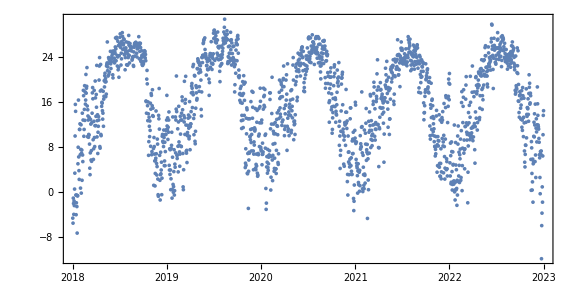

```mathematica
opts={ImageSize->Large,AspectRatio->1/2,PlotTheme->"Detailed",Joined->False};DateListPlot[tsTemp,opts]
```

Data summary

```mathematica
ResourceFunction["RecordsSummary"][tsTemp["Path"]]
```

{1 column 1
Min | 3.72375×10^9
1st Qu | 3.76317×10^9
Mean | 3.80264×10^9
Median | 3.80264×10^9
3rd Qu | 3.8421×10^9
Max | 3.88152×10^9,2 column 2
23.89 °C | 16
24.22 °C | 16
12.78 °C | 14
22.78 °C | 12
25 °C | 12
23.33 °C | 11
(Other) | 1746}

Find regression quantiles for 0.1, 0.5, 0.9

```mathematica
AbsoluteTiming[
qs={0.1,0.5,0.9};
qFuncs=QuantileRegression[QuantityMagnitude[tsTemp["Path"]],16,qs];
]
```

{0.97348,Null}

Plot time series points with fitted regression quantiles

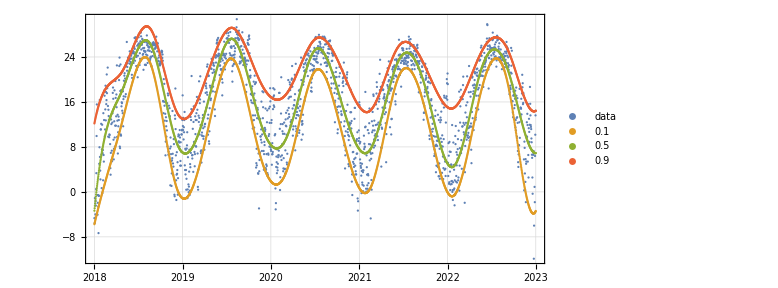

```mathematica
DateListPlot[{tsTemp["Path"],Map[Function[{f},{#,f[#]}&/@tsTemp["Times"]],qFuncs]},opts,Joined->{False,True,True,True},PlotLegends->{"data",Sequence@@qs}]
```

Related Guides

Quantile regression

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/QuantileRegression

AntonAntonov`QuantileRegression`

AntonAntonov/QuantileRegression/tutorial/Quantileregressionoverweathertimeseries

### Keywords

Quantile regression

Temperature data

Weather data